# Pinned Beam

-Graphics-

```mathematica
ClearAll["Global`*"]
$Assumptions= {β>0 && EI>0 &&L>0}
```

{β>0&&EI>0&&L>0}

The differential eigenvalue problem without the boundary conditions:

```mathematica
ODE = D[Y[x],{x,4}]-β^4 Y[x]==0
```

-β^4 Y[x]+Y^(4)[x]==0

General Solution:

```mathematica
sol=Y[x]/.DSolve[ODE,Y[x],x][[1]]//ExpToTrig//Simplify
```

C[1] Cos[x β]+(C[2]+C[4]) Cosh[x β]+C[3] Sin[x β]+(-C[2]+C[4]) Sinh[x β]

Thus, we can write this in the following form:

```mathematica
sol=Cosh[x β] C[2]+Sinh[x β] C[4]+C[1] Cos[x β]+C[3] Sin[x β]
```

C[1] Cos[x β]+C[2] Cosh[x β]+C[3] Sin[x β]+C[4] Sinh[x β]

Now we apply the boundary conditions:

```mathematica
BCs={
(sol==0)/.x->0,
(EI D[sol,{x,2}]==0)/.x->0,
(sol==0)/.x->L,
(EI D[sol,{x,2}]+k D[sol,x]==0)/.x->L}
```

{C[1]+C[2]==0,EI (-β^2 C[1]+β^2 C[2])==0,C[1] Cos[L β]+C[2] Cosh[L β]+C[3] Sin[L β]+C[4] Sinh[L β]==0,k (β C[3] Cos[L β]+β C[4] Cosh[L β]-β C[1] Sin[L β]+β C[2] Sinh[L β])+EI (-β^2 C[1] Cos[L β]+β^2 C[2] Cosh[L β]-β^2 C[3] Sin[L β]+β^2 C[4] Sinh[L β])==0}

```mathematica
C1Rule=Solve[BCs[[1]],C[1]][[1]][[1]]
```

C[1]→-C[2]

```mathematica
C2Rule=Solve[BCs[[2]]/.C1Rule,C[2]][[1]][[1]]
```

C[2]→0

```mathematica
C4Rule=Solve[BCs[[3]]/.C1Rule/.C2Rule,C[4]][[1]][[1]]
```

C[4]→-C[3] Csch[L β] Sin[L β]

Finally, we use the fourth BC to get the characteristic equation:

```mathematica
charEq = Simplify[BCs[[4]]/.C1Rule/.C2Rule/.C4Rule/.k->.5 EI/L/.C[3]->1]
```

(1. L β+0.25 Coth[L β]) Sin[L β]==0.25 Cos[L β]

Now, we define a new variable, z:

```mathematica
charEqz=charEq/.L->z/β
```

(1. z+0.25 Coth[z]) Sin[z]==0.25 Cos[z]

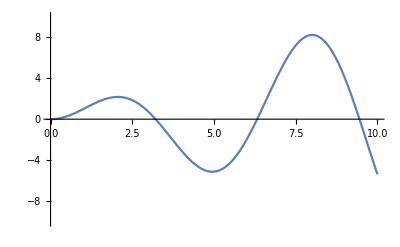

```mathematica
Plot[charEqz,{z,0,10},PlotRange->{-10,10}]
```

```mathematica
roots=FindRoot[charEqz,{z,{3,6,9}}][[1]]
```

z→{3.21363,6.32121,9.45054}

```mathematica
βRule=β->z/L/.roots
```

β→{3.21363/L,6.32121/L,9.45054/L}

```mathematica
ω=z^2 Sqrt[m/EI]/.roots
```

{10.3274 √(m/EI),39.9577 √(m/EI),89.3128 √(m/EI)}

Now our modes have the form:

```mathematica
Φ[x_]=sol/.C1Rule/.C2Rule/.C4Rule//Simplify
```

C[3] (Sin[x β]-Csch[L β] Sin[L β] Sinh[x β])

If we plug in the characteristic values, we get all the modes we solved for:

```mathematica
modes=Φ[x]/.βRule
```

{C[3] (Sin[(3.21363 x)/L]+0.00579763 Sinh[(3.21363 x)/L]),C[3] (Sin[(6.32121 x)/L]-0.000136692 Sinh[(6.32121 x)/L]),C[3] (Sin[(9.45054 x)/L]+4.05238×10^-6 Sinh[(9.45054 x)/L])}

We can normalize them using the norm as:

```mathematica
mags=Chop[Integrate[modes^2,{x,0,L}],10^-6]^(-1/2)
```

{1.39981/(√(L C[3]^2)),1.41014/(√(L C[3]^2)),1.41234/(√(L C[3]^2))}

```mathematica
NModes=Simplify[Thread[modes mags],C[3]>0]
```

{(1.39981 (Sin[(3.21363 x)/L]+0.00579763 Sinh[(3.21363 x)/L]))/(√L),(1.41014 (Sin[(6.32121 x)/L]-0.000136692 Sinh[(6.32121 x)/L]))/(√L),(1.41234 (Sin[(9.45054 x)/L]+4.05238×10^-6 Sinh[(9.45054 x)/L]))/(√L)}

Now, we can plot all of them:

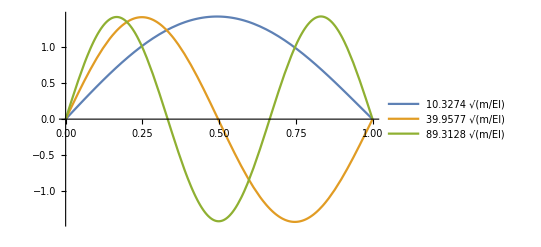

```mathematica
Plot[Evaluate[NModes/.L->1],{x,0,1},PlotLegends-> ω]
```